```mathematica
Energy[x_]:=Module[{χ=x},
Ep1=kbT /ap(ϕ Log[ϕ]+(1-ϕ)Log[1-ϕ]);
Ep2=χ/ap ϕ (1-ϕ);
Eb=κ/2(2/r)^2;
F1=(Ep1+Ep2+Eb)/.ϕ->ϕ1/.r->r1;
F2=(Ep1+Ep2+Eb)/.ϕ->ϕ2/.r->r2;
F=F1 4 Pi r1^2+F2 4 Pi r2^2+α(4 Pi r1^2+4Pi r2^2-4 Pi R0^2)+β(4 Pi r1^2ϕ1+4Pi r2^2ϕ2-4 Pi R0^2 ϕ0);
sub={kbT->0.02,ap->0.01,R0->1,ϕ0->0.2,κ->0.4};
eqr1=Simplify[D[F,r1]]/.sub;
eqr2=Simplify[D[F,r2]]/.sub;
eqϕ1=Simplify[D[F,ϕ1]]/.sub;
eqϕ2=Simplify[D[F,ϕ2]]/.sub;
eqα=Simplify[D[F,α]]/.sub;
eqβ=Simplify[D[F,β]]/.sub;
Sol=Chop[FindRoot[{eqr1==0,eqr2==0,eqϕ1==0,eqϕ2==0,eqα==0,eqβ==0},{{ϕ1,0.98},{ϕ2,0.02},{r1,Sqrt[1/2]},{r2,Sqrt[1/2]},{α,0.01},{β,0.01}}]];
{F/.Sol/.sub,(F1 4 Pi r1^2+F2 4 Pi r2^2)/.Sol/.sub,r1/.Sol,r2/.Sol,ϕ1/.Sol,ϕ2/.Sol}]
```

```mathematica
Energy[0.047]
```

{16.9754,16.9754,0.148195,0.988958,0.813782,0.186218}

```mathematica
data1=Energy/@Table[i,{i,0.047,0.3,0.001}];
```

```mathematica
x=Table[i,{i,0.047,0.3,0.001}]
```

{0.047,0.048,0.049,0.05,0.051,0.052,0.053,0.054,0.055,0.056,0.057,0.058,0.059,0.06,0.061,0.062,0.063,0.064,0.065,0.066,0.067,0.068,0.069,0.07,0.071,0.072,0.073,0.074,0.075,0.076,0.077,0.078,0.079,0.08,0.081,0.082,0.083,0.084,0.085,0.086,0.087,0.088,0.089,0.09,0.091,0.092,0.093,0.094,0.095,0.096,0.097,0.098,0.099,0.1,0.101,0.102,0.103,0.104,0.105,0.106,0.107,0.108,0.109,0.11,0.111,0.112,0.113,0.114,0.115,0.116,0.117,0.118,0.119,0.12,0.121,0.122,0.123,0.124,0.125,0.126,0.127,0.128,0.129,0.13,0.131,0.132,0.133,0.134,0.135,0.136,0.137,0.138,0.139,0.14,0.141,0.142,0.143,0.144,0.145,0.146,0.147,0.148,0.149,0.15,0.151,0.152,0.153,0.154,0.155,0.156,0.157,0.158,0.159,0.16,0.161,0.162,0.163,0.164,0.165,0.166,0.167,0.168,0.169,0.17,0.171,0.172,0.173,0.174,0.175,0.176,0.177,0.178,0.179,0.18,0.181,0.182,0.183,0.184,0.185,0.186,0.187,0.188,0.189,0.19,0.191,0.192,0.193,0.194,0.195,0.196,0.197,0.198,0.199,0.2,0.201,0.202,0.203,0.204,0.205,0.206,0.207,0.208,0.209,0.21,0.211,0.212,0.213,0.214,0.215,0.216,0.217,0.218,0.219,0.22,0.221,0.222,0.223,0.224,0.225,0.226,0.227,0.228,0.229,0.23,0.231,0.232,0.233,0.234,0.235,0.236,0.237,0.238,0.239,0.24,0.241,0.242,0.243,0.244,0.245,0.246,0.247,0.248,0.249,0.25,0.251,0.252,0.253,0.254,0.255,0.256,0.257,0.258,0.259,0.26,0.261,0.262,0.263,0.264,0.265,0.266,0.267,0.268,0.269,0.27,0.271,0.272,0.273,0.274,0.275,0.276,0.277,0.278,0.279,0.28,0.281,0.282,0.283,0.284,0.285,0.286,0.287,0.288,0.289,0.29,0.291,0.292,0.293,0.294,0.295,0.296,0.297,0.298,0.299,0.3}

```mathematica
y=data1[[All,1]]
```

{16.9754,17.1595,17.3315,17.4924,17.643,17.784,17.9161,18.0401,18.1563,18.2654,18.3679,18.4642,18.5548,18.6399,18.72,18.7955,18.8665,18.9334,18.9965,19.056,19.112,19.1649,19.2149,19.262,19.3065,19.3485,19.3883,19.4258,19.4613,19.4948,19.5265,19.5565,19.5849,19.6118,19.6372,19.6613,19.6841,19.7057,19.7261,19.7455,19.7638,19.7812,19.7977,19.8133,19.8281,19.8422,19.8555,19.8681,19.8801,19.8915,19.9022,19.9125,19.9222,19.9314,19.9401,19.9484,19.9563,19.9638,19.9708,19.9776,19.984,19.99,19.9958,20.0013,20.0065,20.0114,20.0161,20.0206,20.0248,20.0288,20.0327,20.0363,20.0397,20.043,20.0461,20.0491,20.0519,20.0546,20.0571,20.0595,20.0618,20.064,20.0661,20.0681,20.0699,20.0717,20.0734,20.075,20.0765,20.078,20.0794,20.0807,20.0819,20.0831,20.0843,20.0853,20.0864,20.0873,20.0883,20.0891,20.09,20.0908,20.0915,20.0922,20.0929,20.0936,20.0942,20.0948,20.0953,20.0959,20.0964,20.0968,20.0973,20.0977,20.0982,20.0985,20.0989,20.0993,20.0996,20.0999,20.1002,20.1005,20.1008,20.1011,20.1013,20.1016,20.1018,20.102,20.1022,20.1024,20.1026,20.1028,20.1029,20.1031,20.1032,20.1034,20.1035,20.1037,20.1038,20.1039,20.104,20.1041,20.1042,20.1043,20.1044,20.1045,20.1046,20.1047,20.1047,20.1048,20.1049,20.1049,20.105,20.1051,20.1051,20.1052,20.1052,20.1053,20.1053,20.1053,20.1054,20.1054,20.1055,20.1055,20.1055,20.1056,20.1056,20.1056,20.1057,20.1057,20.1057,20.1057,20.1058,20.1058,20.1058,20.1058,20.1058,20.1058,20.1059,20.1059,20.1059,20.1059,20.1059,20.1059,20.106,20.106,20.106,20.106,20.106,20.106,20.106,20.106,20.106,20.106,20.106,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1061,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062,20.1062}

```mathematica
data2=Energy/@Table[i,{i,0.0465,0.047,0.000005}];
```

```mathematica
x2=Table[i,{i,0.0465,0.047,0.000005}];
```

```mathematica
y2=data2[[All,3]];
```

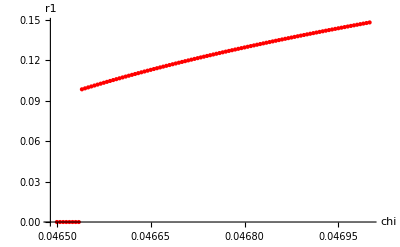

```mathematica
ListPlot[Transpose[{x2,y2}],PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"chi","r1"}]
```

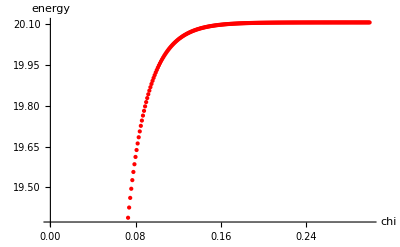

```mathematica
l1=ListPlot[Transpose[{x,y}],PlotStyle->{Red,PointSize[Medium]},AxesLabel->{"chi","energy"}]
```

```mathematica
EnergyUniform=(kbT /ap(ϕ0 Log[ϕ0]+(1-ϕ0)Log[1-ϕ0])+χ/ap ϕ0 (1-ϕ0))4 Pi R0^2+16 Pi κ/.sub
```

20.1062+4 π (-1.0008+16. χ)

```mathematica
EnergyUniform/.χ->0
```

7.52971

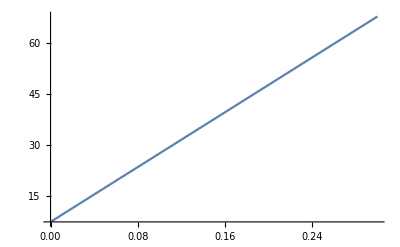

```mathematica
l2=Plot[EnergyUniform,{χ,0,0.3}]
```

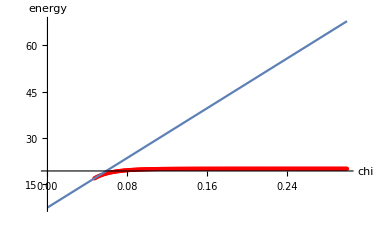

```mathematica
Show[l1,l2,PlotRange->All]
```